```mathematica
Clear[L]
θq=π/2;
ϕq=0;
q=2π/L
Clear[q]
m[s_]:={Cos[q s], 0, Sin[q s]}
```

(2 π)/L

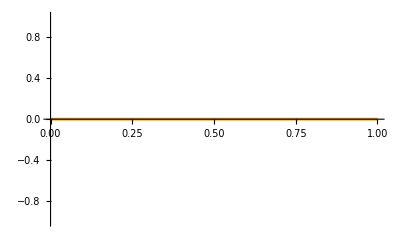

```mathematica
Plot[Evaluate@(m[s]/.L->1),{s,0,1},PlotRange->Full]
```

```mathematica
sfy[qy_]=Integrate[ⅇ^(ⅈ(y2-y1)qy),{y1,0,L},{y2,0,L}];
```

```mathematica
sf[qx_,qy_]=Table[sfy[qy]*Integrate[ⅇ^(ⅈ(x2-x1)qx)m[x1][[i]]m[x2][[j]],{x1,0,L},{x2,0,L}],{i,3},{j,3}]//FullSimplify;
```

```mathematica
ContourPlot[Im[sf[2π qx,2π qy][[3,1]]/.L->1],{qx,-2,2},{qy,-2,2},PlotRange->Full,PlotPoints->1000]
```

-Graphics-

```mathematica
ContourPlot[Re[sf[2π qx,2π qy][[1,1]]/.L->1],{qx,-2,2},{qy,-2,2},PlotRange->Full,PlotPoints->1000]
```

-Graphics-

```mathematica
ContourPlot[Re[sf[2π qx,2π qy][[3,3]]/.L->1],{qx,-2,2},{qy,-2,2},PlotRange->Full,PlotPoints->1000]
```

-Graphics-

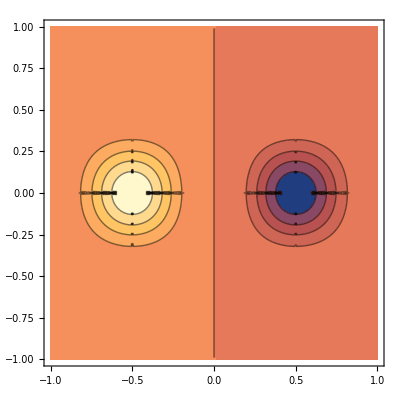

```mathematica
ContourPlot[Im[sf[2q qx,2q qy][[3,1]]/.L->1],{qx,-1,1},{qy,-1,1},PlotRange->Full,PlotPoints->100]
```

```mathematica
Manipulate[Plot[Evaluate@ReIm[(sf[ 2 q*qx,10^-6][[1,{1,3}]]/.q->qq π/L/.L->ll)],{qx,-1,1},PlotRange->Full],{qq,0.01,1000},{ll,0.01,100}]
```